```mathematica
Clear[T,T0]
ft=Integrate[1/(Exp[-t/T0]+1)1/(Exp[(t-T/2)/T0]+1),t]//FullSimplify
(*T0 = .01 T;*)
((ft/.t->T)-(ft/.t->0))/T//FullSimplify
```

(ⅇ^(T/(2 T0)) T0 (Log[1+ⅇ^(t/T0)]-Log[ⅇ^(t/T0)+ⅇ^(T/(2 T0))]))/(-1+ⅇ^(T/(2 T0)))

(ⅇ^(T/(2 T0)) T0 (Log[1+ⅇ^(T/(2 T0))]+Log[1+ⅇ^(T/T0)]-Log[2 ⅇ^(T/(2 T0))+2 ⅇ^(T/T0)]))/((-1+ⅇ^(T/(2 T0))) T)

```mathematica
(T0 (Log[1+ⅇ^(T/T0)]-Log[2]-T/(2 T0)))/((1-ⅇ^(-T/(2 T0))) T)
FullSimplify[(T0 (Log[1+ⅇ^(T/T0)]-Log[2]-T/(2 T0)))/((1-ⅇ^(-T/(2 T0))) T),T>0&&T0>0]
```

(T0 (-T/(2 T0)-Log[2]+Log[1+ⅇ^(T/T0)]))/((1-ⅇ^(-T/(2 T0))) T)

(T0 (-T/(2 T0)+Log[1/2 (1+ⅇ^(T/T0))]))/(T-ⅇ^(-T/(2 T0)) T)

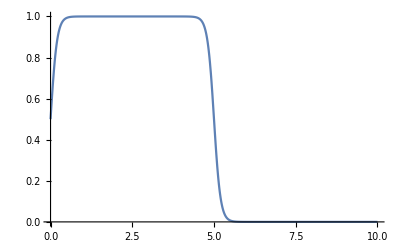

```mathematica
T = 10;
T0=.01 T;
Plot[1/(Exp[-t/T0]+1)1/(Exp[(t-T/2)/T0]+1),{t,0,T}]
```